NDSolveValue::berr: The scaled boundary value residual error of 4.42753 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

NDSolveValue::berr: The scaled boundary value residual error of 1.00538 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

NDSolveValue::berr: The scaled boundary value residual error of 82.0692 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

General::stop: Further output of NDSolveValue::berr will be suppressed during this calculation.

3.63336

{-3.97944,-2.72789,-2.90315,-2.84925,-2.86483,-2.86023,-2.86158,-2.86118,-2.8613,-2.86126}

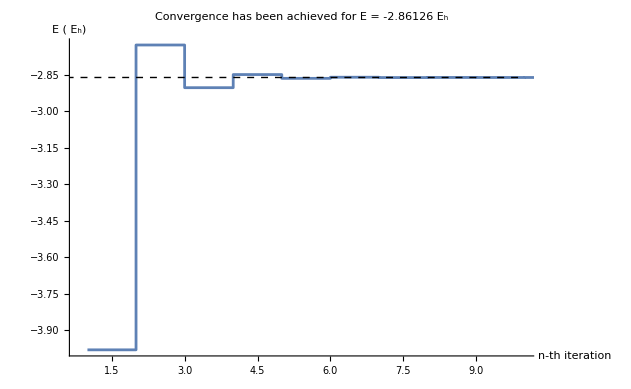

```mathematica
prevE=1.;
currE=0.;
prec=10^-4;

rho=0;
rMin=$MachineEpsilon;
rMax=50.;

n=1;
l=0;

vNuc=-2/r;

{t,vals}=Reap[While[Abs[prevE-currE]>prec,
prevE=currE;
uHart=NDSolveValue[{uH''[r]==-rho/r,uH[rMin]==0,uH[rMax]==1},uH,{r,rMin,rMax},Method->"Adams"];
alpha=(2-uHart[rMax])/rMax;
vHart=uHart[r]/r+alpha;
vHart/=2.;
(*vX=((-3 rho)/(4 Pi^2 r^2))^(1/3);
rs=(3r^2/rho)^(1/3);
ec=a Log[rs]+b-a/3+c*2/3 rs Log[rs]+(2d-c)rs/3;
vE=Piecewise[{{a,rs<=1}}];*)
vX=0.;
vE=0.;
Vtot=vNuc+vHart+(vX+vE)/2.;
{gden,gdefun}=NDEigensystem[{-1/2psi''[r]+(Vtot+(l(l+1))/(2r^2))psi[r],DirichletCondition[psi[r]==0,True]},psi,{r,rMin,rMax},All,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.15}}}]//Transpose//Sort//First;
gdNorm=NIntegrate[gdefun[r],{r,rMin,rMax},AccuracyGoal->4];
gdefunN=gdefun[r]/Sqrt[1];
rho=2 gdefunN^2;
Ehart=NIntegrate[vHart rho,{r,rMin,rMax},Method->"GlobalAdaptive",AccuracyGoal->4]/2.;
currE=2 gden-Ehart;
Sow[currE]
]]//Last//First//AbsoluteTiming;
t
vals
ListStepPlot[vals,PlotRange->All,PlotLabel->StringForm["Convergence has been achieved for E = ``  E_h",Last[vals]],Epilog->{Dashed,Line[{{0,Last[vals]},{Length@vals,Last[vals]}}]} ,AxesLabel->{"n-th iteration","E ( E_h)"}]
```